```mathematica
ClearAll["Global`*"]
T=1/2 M Yt^2+1/2 m (yt^2+zt^2);
V=m g z;
F = F0 Sin[ωf t];
τ=c θt;
```

```mathematica
y=Y+l Sin[θ];z=-l Cos[θ];
yt=Yt+l Cos[θ] θt;zt=l Sin[θ] θt;
T
V
F
```

1/2 m (θt^2 l^2 sin^2(θ)+(θt l cos(θ)+Yt)^2)+(M Yt^2)/2

-g l m cos(θ)

F0 sin(t ωf)

```mathematica
(*First E-L equation, Y*)
L=T-V;
D[L,Yt];
D[%,Y] Yt+D[%,Yt] Ytt+D[%,θ] θt+D[%,θt] θtt;
D[L,Y];
eqn1=Collect[%%-%,{Ytt,θtt},Simplify]
```

θt^2 (-l) m sin(θ)+θtt l m cos(θ)+Ytt (m+M)

```mathematica
(*Second E-L equation, θ *)
D[L,θt];
D[%,Y] Yt+D[%,Yt] Ytt+D[%,θ] θt+D[%,θt] θtt;
D[L,θ];
eqn2=Collect[%%-%,{Ytt,θtt},Simplify]+ τ
```

c θt+g l m sin(θ)+θtt l^2 m+l m Ytt cos(θ)

```mathematica
leqn1=eqn1/.{Cos[θ]->1,Sin[θ]->θ}
```

θ θt^2 (-l) m+θtt l m+Ytt (m+M)

```mathematica
leqn1=%-%[[2]]
```

θtt l m+Ytt (m+M)

```mathematica
leqn2=eqn2/.{Cos[θ]->1,Sin[θ]->θ}
```

c θt+g θ l m+θtt l^2 m+l m Ytt

```mathematica
(*nleqn1 = Collect[leqn1/.{Ytt->s^2 Y,θ->Θ,θt->s Θ,θtt->s^2 Θ},{Y,Θ},Simplify]
nleqn2 =Collect[leqn2/.{Ytt->s^2 Y,θ->Θ,θt->s Θ,θtt->s^2 Θ},{Y,Θ},Simplify]*)
nleqn1 = Collect[leqn1/.{Ytt->s^2 Y,θ->Θ,θt->s Θ,θtt->s^2 Θ},{Y,Θ},Simplify]
nleqn2 =Collect[leqn2/.{Ytt->s^2Y,θ->Θ,θt->s Θ,θtt->s^2 Θ},{Y,Θ},Simplify]
```

Θ l m s^2+s^2 Y (m+M)

Θ (s (c+l^2 m s)+g l m)+l m s^2 Y

```mathematica
A = {{nleqn1[[1]] /. {Y ->1},  nleqn1[[2]] /. {Θ->1}},
{nleqn2[[1]] /. {Y->1}, nleqn2[[2]] /. {Θ->1}}}
```

((m+M) s^2 | l m s^2
l m s^2 | g l m+s (m s l^2+c))

```mathematica
cp=Collect[Det[A],w,Simplify]
```

s^2 (s (c (m+M)+l^2 m M s)+g l m (m+M))

```mathematica
(*cp=Collect[cp/w^2,w,Simplify] *)
```

```mathematica
soln=Solve[cp ==0,s]
```

{{s→0},{s→0},{s→(-√(m+M) √(c^2 m+c^2 M-4 g l^3 m^2 M)-c m-c M)/(2 l^2 m M)},{s→(√(m+M) √(c^2 m+c^2 M-4 g l^3 m^2 M)-c m-c M)/(2 l^2 m M)}}

```mathematica
parameters={m->1,M->10,l->1,g->981/100, c->4};
s1 = soln[[3,1]] /.parameters
s2 = soln[[4,1]]/.parameters
```

s→1/20 (-44-ⅈ √(11902/5))

s→1/20 (-44+ⅈ √(11902/5))

```mathematica
w1 = (-45000-4500 ⅈ √9710)/225000/ I
```

-(ⅈ (-45000-4500 ⅈ √9710))/225000

```mathematica
w2 = (-45000+4500 ⅈ √9710)/225000 / I
```

-(ⅈ (-45000+4500 ⅈ √9710))/225000

```mathematica
f = {{F0},{0}}
```

(F0
0)

```mathematica
(Inverse[A] /.parameters) . f
```

((F0 (s (s+4)+981/100))/(10 s^4+44 s^3+(10791 s^2)/100)
-(F0 s^2)/(10 s^4+44 s^3+(10791 s^2)/100))

```mathematica
Yfunc = Simplify[(((Inverse[A].f /. parameters) Exp[s t] /. {s-> I wf}))[[1,1]]]
Θfunc = Simplify[(((Inverse[A].f /. parameters)Exp[s t]/. {s-> I wf}))[[2,1]]]
```

-(F0 (100 wf^2-400 ⅈ wf-981) ⅇ^(ⅈ t wf))/(wf^2 (1000 wf^2-4400 ⅈ wf-10791))

-(100 F0 ⅇ^(ⅈ t wf))/(-1000 wf^2+4400 ⅈ wf+10791)

```mathematica
ComplexExpand[Yfunc]
```

(1600000 sin(4 t))/336893681-(156921855 cos(4 t))/2695149448+ⅈ (-(156921855 sin(4 t))/2695149448-(1600000 cos(4 t))/336893681)

```mathematica
ComplexExpand[Θfunc]
```

-(440000 F0 wf sin(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)+(100000 F0 wf^2 cos(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)-(1079100 F0 cos(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)+ⅈ ((100000 F0 wf^2 sin(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)-(1079100 F0 sin(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)+(440000 F0 wf cos(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2))

```mathematica
yp = {(40000 F0 wf Sin[t wf])/(19360000 wf^2+(1000 wf^2-10791)^2)-(100000 F0 wf^2 Cos[t wf])/(19360000 wf^2+(1000 wf^2-10791)^2)+(300100 F0 Cos[t wf])/(19360000 wf^2+(1000 wf^2-10791)^2)-(10585971 F0 Cos[t wf])/((19360000 wf^2+(1000 wf^2-10791)^2) wf^2),-(440000 F0 wf Sin[t wf])/(19360000 wf^2+(10791-1000 wf^2)^2)+(100000 F0 wf^2 Cos[t wf])/(19360000 wf^2+(10791-1000 wf^2)^2)-(1079100 F0 Cos[t wf])/(19360000 wf^2+(10791-1000 wf^2)^2)}
```

{(40000 F0 wf sin(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)-(100000 F0 wf^2 cos(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)+(300100 F0 cos(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)-(10585971 F0 cos(t wf))/((19360000 wf^2+(1000 wf^2-10791)^2) wf^2),-(440000 F0 wf sin(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)+(100000 F0 wf^2 cos(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)-(1079100 F0 cos(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)}

```mathematica
Yfunc /. {F0->100}
```

-(100 (100 wf^2-400 ⅈ wf-981) ⅇ^(ⅈ t wf))/(wf^2 (1000 wf^2-4400 ⅈ wf-10791))

```mathematica
ComplexExpand[Yfunc]
```

(40000 F0 wf sin(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)-(100000 F0 wf^2 cos(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)+(300100 F0 cos(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)-(10585971 F0 cos(t wf))/((19360000 wf^2+(1000 wf^2-10791)^2) wf^2)+ⅈ (-(100000 F0 wf^2 sin(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)+(300100 F0 sin(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)-(10585971 F0 sin(t wf))/((19360000 wf^2+(1000 wf^2-10791)^2) wf^2)-(40000 F0 wf cos(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2))

```mathematica
yp
```

{(40000 F0 wf sin(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)-(100000 F0 wf^2 cos(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)+(300100 F0 cos(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)-(10585971 F0 cos(t wf))/((19360000 wf^2+(1000 wf^2-10791)^2) wf^2),-(440000 F0 wf sin(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)+(100000 F0 wf^2 cos(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)-(1079100 F0 cos(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)}

```mathematica
Clear[F0, wf]
```

```mathematica
F0 = 100
```

100

```mathematica
wf=1
```

2

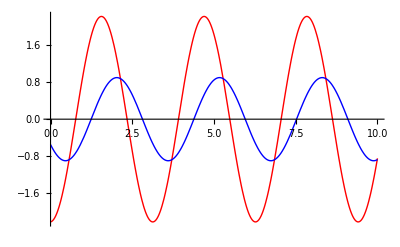

```mathematica
Plot[yp , {t,0,10}, PlotStyle->{Red, Blue}]
```